```mathematica
(*EP1 - Pedro Trama Fernandes Pereira|RA:254344*)
(*Inicialmente, iremos definir a função f(x)=x Exp(-x^2) Sin(x) e plotar seu gráfico*)
f[x_]:=x*Exp[-x^2]*Sin[x]
Plot[f[x], {x, 0, 5},PlotStyle->{Magenta,Thick}]
```

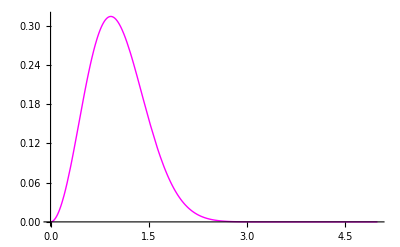

```mathematica
(*Com o gráfico em mãos, podemos partir para sua discretização usando a fórmula vista em aula*)
```

```mathematica
xi=0;xf=5.;Np=101;Ni=Np-1;Δx=((xf-xi)/(Ni))(*A escolha de xf=5. é arbitrária, já a de Np=101 serve para termos uma boa representação discreta*)
```

```mathematica
0.05 (*Esse é o valor do Δx, ou seja, o tamanho do intervalo entre os pontos do gráfico discretizado*)
```

```mathematica
(*A partir daqui, criamos uma lista para todos os 101 valores de x com intervalo de 0.05 entre cada número*)
x=Table[i*Δx,{i,0,Ni}]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.}

```mathematica
(*Agora que temos todos os valores de x do gráfico, precisamos dos seus pares no eixo y, ou seja, f(x). Para isso, iremos criar outra lista, dessa vez, com os valores de f(x)*)
```

```mathematica
fx=f[x]
```

{0.,0.00249272,0.00988401,0.021917,0.0381759,0.0581036,0.0810255,0.106177,0.132736,0.159854,0.186688,0.212437,0.236363,0.257818,0.276265,0.29129,0.302605,0.310058,0.313622,0.31339,0.30956,0.30242,0.292331,0.279706,0.264991,0.248647,0.231134,0.212892,0.194332,0.175828,0.157703,0.140231,0.123635,0.108082,0.0936921,0.0805379,0.0686514,0.0580292,0.0486384,0.0404228,0.0333087,0.0272102,0.0220342,0.0176842,0.0140642,0.0110812,0.00864723,0.0066809,0.0051083,0.00386344,0.00288831,0.00213269,0.00155372,0.00111528,0.000787356,0.000545329,0.000369248,0.00024316,0.000154466,0.0000933454,0.0000522468,0.0000254407,8.64337×10^-6,-1.2992×10^-6,-6.67106×10^-6,-9.09611×10^-6,-9.7052×10^-6,-9.26701×10^-6,-8.28887×10^-6,-7.09328×10^-6,-5.87489×10^-6,-4.74225×10^-6,-3.74783×10^-6,-2.909×10^-6,-2.22255×10^-6,-1.67428×10^-6,-1.24515×10^-6,-9.15085×10^-7,-6.65099×10^-7,-4.78375×10^-7,-3.40668×10^-7,-2.40301×10^-7,-1.67955×10^-7,-1.16352×10^-7,-7.99098×10^-8,-5.44205×10^-8,-3.67568×10^-8,-2.46257×10^-8,-1.63669×10^-8,-1.07924×10^-8,-7.06121×10^-9,-4.58436×10^-9,-2.95351×10^-9,-1.88832×10^-9,-1.19812×10^-9,-7.54427×10^-10,-4.71441×10^-10,-2.92365×10^-10,-1.79927×10^-10,-1.09882×10^-10,-6.65874×10^-11}

```mathematica
(*Por último, basta unir as duas listas para termos as coordenadas do gráfico desejado*)
xfx=Table[{x[[i]],fx[[i]]},{i,1,Np}]
```

{{0.,0.},{0.05,0.00249272},{0.1,0.00988401},{0.15,0.021917},{0.2,0.0381759},{0.25,0.0581036},{0.3,0.0810255},{0.35,0.106177},{0.4,0.132736},{0.45,0.159854},{0.5,0.186688},{0.55,0.212437},{0.6,0.236363},{0.65,0.257818},{0.7,0.276265},{0.75,0.29129},{0.8,0.302605},{0.85,0.310058},{0.9,0.313622},{0.95,0.31339},{1.,0.30956},{1.05,0.30242},{1.1,0.292331},{1.15,0.279706},{1.2,0.264991},{1.25,0.248647},{1.3,0.231134},{1.35,0.212892},{1.4,0.194332},{1.45,0.175828},{1.5,0.157703},{1.55,0.140231},{1.6,0.123635},{1.65,0.108082},{1.7,0.0936921},{1.75,0.0805379},{1.8,0.0686514},{1.85,0.0580292},{1.9,0.0486384},{1.95,0.0404228},{2.,0.0333087},{2.05,0.0272102},{2.1,0.0220342},{2.15,0.0176842},{2.2,0.0140642},{2.25,0.0110812},{2.3,0.00864723},{2.35,0.0066809},{2.4,0.0051083},{2.45,0.00386344},{2.5,0.00288831},{2.55,0.00213269},{2.6,0.00155372},{2.65,0.00111528},{2.7,0.000787356},{2.75,0.000545329},{2.8,0.000369248},{2.85,0.00024316},{2.9,0.000154466},{2.95,0.0000933454},{3.,0.0000522468},{3.05,0.0000254407},{3.1,8.64337×10^-6},{3.15,-1.2992×10^-6},{3.2,-6.67106×10^-6},{3.25,-9.09611×10^-6},{3.3,-9.7052×10^-6},{3.35,-9.26701×10^-6},{3.4,-8.28887×10^-6},{3.45,-7.09328×10^-6},{3.5,-5.87489×10^-6},{3.55,-4.74225×10^-6},{3.6,-3.74783×10^-6},{3.65,-2.909×10^-6},{3.7,-2.22255×10^-6},{3.75,-1.67428×10^-6},{3.8,-1.24515×10^-6},{3.85,-9.15085×10^-7},{3.9,-6.65099×10^-7},{3.95,-4.78375×10^-7},{4.,-3.40668×10^-7},{4.05,-2.40301×10^-7},{4.1,-1.67955×10^-7},{4.15,-1.16352×10^-7},{4.2,-7.99098×10^-8},{4.25,-5.44205×10^-8},{4.3,-3.67568×10^-8},{4.35,-2.46257×10^-8},{4.4,-1.63669×10^-8},{4.45,-1.07924×10^-8},{4.5,-7.06121×10^-9},{4.55,-4.58436×10^-9},{4.6,-2.95351×10^-9},{4.65,-1.88832×10^-9},{4.7,-1.19812×10^-9},{4.75,-7.54427×10^-10},{4.8,-4.71441×10^-10},{4.85,-2.92365×10^-10},{4.9,-1.79927×10^-10},{4.95,-1.09882×10^-10},{5.,-6.65874×10^-11}}

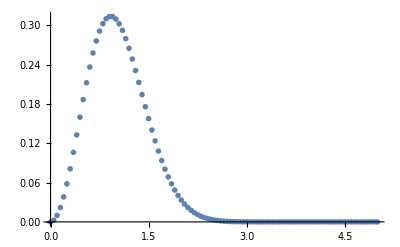

```mathematica
(*Enfim, podemos plotar o gráfico discretizado*)
ListPlot[xfx,PlotMarkers->{Magenta,Tiny}]
```

```mathematica
(*Uma parte importante da discretização é o cálculo do erro, que representa a diferença entre o valor exato e o aproximado. A seguir, calculamos o erro para o gráfico anterior*)
```

```mathematica
ϵ[xa_]:=Abs[f[∞]-f[xa]]
```

```mathematica
LogPlot[e[xa],{xa,1,3},PlotStyle->{Magenta,Thick}]
```

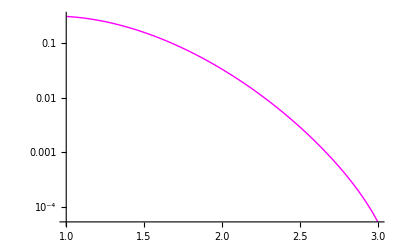

```mathematica
(*Aqui iremos calcular o erro usando os valores de x que se aproximam do infinito*)
```

```mathematica
Clear [ϵ]
```

```mathematica
ϵ[xa_]:=Abs[Limit[f[z],z->∞]-f[xa]]
LogPlot[ϵ[xa],{xa,1,5},PlotStyle->{Magenta,Thick}]
```

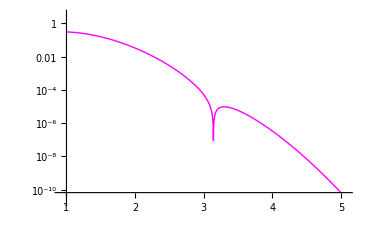

```mathematica
(*Usando a função de ver as coordenadas do gráfico, podemos facilmente encontrar os valores para as precisões de 10^-2,10^-4,10^-6 e 10^-8
10^-2: 2.0
10^-4: 3.0
10^-6: 3.5
10^-8: 4.2
 *)
```